# CKT Classic 1

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pcs/Desktop/Breaking time reversal symmetry/Klein group

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[F,Fun,Funinv];
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Funinv[α_,k_,s_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},-1].s
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

Clear[mapeoinv];
mapeoinv[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funinv[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

```mathematica
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
```

## Symmetry lines

```mathematica
Clear[rot];
rot[θ_]:={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
Clear[Tx,Ty,Tz];
Tx=DiagonalMatrix[{1,-1,-1}];
Ty=DiagonalMatrix[{-1,1,-1}];
Tz=DiagonalMatrix[{-1,-1,1}];
Clear[T1,T2,T3];
T1[α_]:={{-Cos[α],-Sin[α],0},{-Sin[α],Cos[α],0},{0,0,1}};
T2[α_]:={{Cos[α],Sin[α],0},{Sin[α],-Cos[α],0},{0,0,1}};
T3=Tz;
Clear[Rz];
Rz[α_]:={{Cos[α],-Sin[α],0},{Sin[α],Cos[α],0},{0,0,1}};
Clear[com];
com[a_,b_]:=a.b-b.a;
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];
```

## Poincare maps

```mathematica
Clear[Rx,Rz,Rxx,Rzz];
Rz[α_,τ_]:={{Cos[α*τ],-Sin[α*τ],0},{Sin[α*τ],Cos[α*τ],0},{0,0,1}};
Rxx[k_,s_]:={{1,0,0},{0,Cos[k*s[[1]]],-Sin[k*s[[1]]]},{0,Sin[k*s[[1]]],Cos[k*s[[1]]]}};
Rx[k_]:={{1,0,0},{0,Cos[k],-Sin[k]},{0,Sin[k],Cos[k]}};
Rzz[α_,τ_,s_]:={{Cos[α*τ*s[[3]]],-Sin[α*τ*s[[3]]],0},{Sin[α*τ*s[[3]]],Cos[α*τ*s[[3]]],0},{0,0,1}};
Clear[map1,map2];
map1[α_,τ_,k_,s_,n_]:=NestList[Rz[α,τ].Rxx[k,#].#&,s,n];
map2[α_,τ_,k_,s_,n_]:=NestList[Rx[k].Rzz[α,τ,#].#&,s,n];
```

```mathematica
τ=1;
α=0.84;
k=1.3;
```

```mathematica
ini=RandomPoint[Disk[{0,0},1.999],50];
```

```mathematica
ini=Table[{i,0},{i,-1.999,1.999,0.001}];
ini=Map[rot[α/2].#&,ini];
```

```mathematica
ini=Table[{0,i},{i,-1.999,1.999,0.001}];
ini=Map[rot[α/2].#&,ini];
```

```mathematica
ini=Table[{i,0},{i,-1.999,1.999,0.001}];
```

```mathematica
kicks=2000;
poincare=ParallelTable[mapeo[i,α,k,kicks],{i,ini},DistributedContexts->Full];
poincare=Flatten[poincare,1];
```

```mathematica
Clear[T1,T2,T3];
T1[α_]:={{-Cos[α],-Sin[α]},{-Sin[α],Cos[α]}};
T2[α_]:={{Cos[α],Sin[α]},{Sin[α],-Cos[α]}};
```

```mathematica
poincare1=Map[T1[α].#&,poincare];
poincare2=Map[T2[α].#&,poincare];
```

```mathematica
ListPlot[{poincare,poincare1,poincare2},PlotRange->All,AspectRatio->1,ImageSize->800,PlotLegends->{Style["original",18],Style["T1",18],Style["T2",18]}]
```

-Graphics-

# QKT Quantum

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pcs/Desktop/Breaking time reversal symmetry/Klein group

```mathematica
(*Operators*)
Clear[Sz,SM,Sm,Sx,Sy];
Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
Qp[J_]:=DiagonalMatrix[Table[Sqrt[i/2],{i,IntegerPart[2J]}],-1];
QQ[J_]:=Qp[J]+Transpose[Qp[J]];
PP[J_]:=-I(Qp[J]-Transpose[Qp[J]]);
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
Clear[haar];
haar[dim_Integer]:=Module[{l=2*dim+1,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

## Method

```mathematica
radius=1.99;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region=circlePoints;
region//Length
```

19906

```mathematica
ListPlot[region,AspectRatio->1]
```

## Phase space

```mathematica
Clear[a2iM];
a2iM[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J,2}],18]]
];
Clear[a2im];
a2im[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J+1,J,2}],18]]
];
cohesM=ParallelTable[Quiet[a2iM[J,i[[1 ]],i[[2]]]],{i,region}];
cohesm=ParallelTable[Quiet[a2im[J,i[[1]],i[[2]]]],{i,region}];
Clear[husimiM,husimim];
husimiM[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohesM[[i]]].ψ]^2},{i,Length[region]}];
husimim[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohesm[[i]]].ψ]^2},{i,Length[region]}];
```

```mathematica
Clear[J];
J=207;
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1 ]],i[[2]]]],{i,region},DistributedContexts->Full,Method->"CoarsestGrained"];
```

```mathematica
Clear[Floq];
(*Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*α*τ/(2J))(Sz[J].Sz[J])].MatrixExp[(-I*k)(Sx[J])]];*)
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
```

```mathematica
Clear[Rz,Rx,Ry];
Rx[J_,θ_]:=MatrixExp[-I(N[θ])Sx[J]];
Ry[J_,θ_]:=MatrixExp[-I(N[θ])Sy[J]];
Rz[J_,θ_]:=MatrixExp[-I(N[θ])Sz[J]];
```

```mathematica
τ2=1;
α2=0.84;
k2=1.3;
```

```mathematica
mat=Floq[J,α2,k2,τ2];
(*mat=Rx[J,Pi/2].Ry[J,Pi/2].(Rx[J,k2/2].Floq[J,α2,k2,τ2].ConjugateTranspose[Rx[J,k2/2]]).ConjugateTranspose[Ry[J,Pi/2]].ConjugateTranspose[Rx[J,Pi/2]];*)
{eigenval,eigenvec}=Eigensystem[mat];
eigenvec=Orthogonalize[eigenvec];
(*South pole*)
(*mat=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;*)
(*matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];*)
(*zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
eigenval=Riffle[eigenvalM,eigenvalm];
eigenvec=Riffle[neweigenvecM,neweigenvecm];*)
```

```mathematica
q=2;
d2M=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^(2q)],{i,cohes},DistributedContexts->Full,Method->"CoarsestGrained"];
newd2M=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2M]/Log[2J+1]}];
```

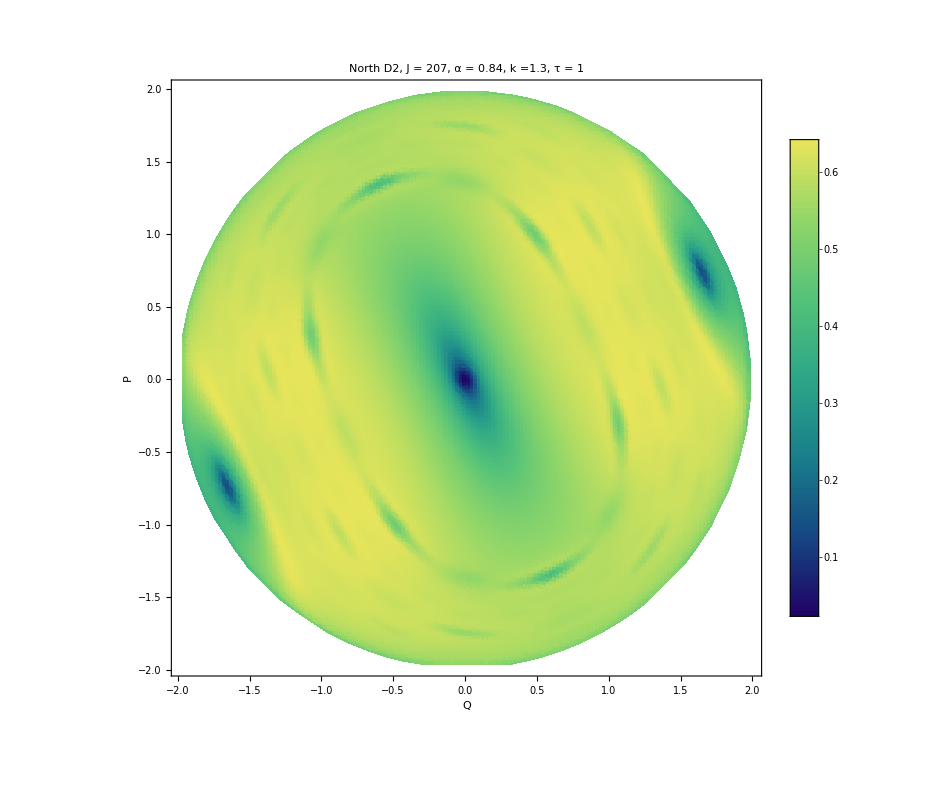

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->1, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α2]]<>", k ="<>ToString[k2]<>", τ = "<>ToString[τ2],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
```

```mathematica
Clear[rotation,t1,t2];
rotation=MatrixExp[(-I)(α2)(Sz[J])];
t1[state_]:=Conjugate[rotation.state];
t2[state_]:=rotation.Conjugate[state];
```

```mathematica
Clear[husimi];
husimi[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohes[[i]]].ψ]^2},{i,Length[region]},DistributedContexts->Full];
```

```mathematica
inicohe1=t1[a2[J,75/100,1]];
inicohe2=t2[a2[J,75/100,1]];
(*inicohe=t1[a2[J,1/2,1]];*)
ipr=ParallelTable[Abs[Conjugate[i].inicohe1]^2,{i,eigenvec}];
sorted=SortBy[Transpose[{ipr,eigenval,eigenvec}],First];
sortedeigenvec=sorted[[All,3]];
```

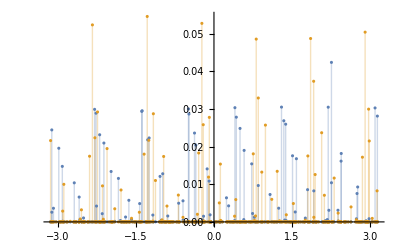

```mathematica
ListPlot[{Transpose[{Arg[sorted[[All,2]]],Abs[Conjugate[sortedeigenvec].inicohe1]^2}],Transpose[{Arg[sorted[[All,2]]],Abs[Conjugate[sortedeigenvec].inicohe2]^2}]},PlotRange->All,Filling->Bottom]
```

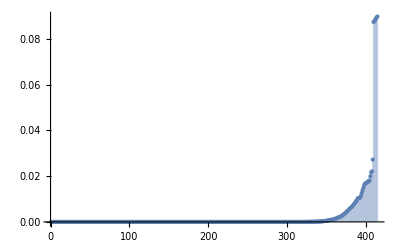

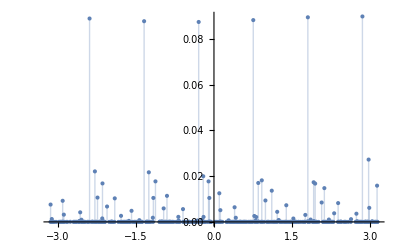

```mathematica
ListPlot[sorted[[All,1]],Filling->Bottom,PlotRange->All]
ListPlot[Transpose[{Arg[sorted[[All,2]]],Abs[Conjugate[sortedeigenvec].inicohe]^2}],PlotRange->All,Filling->Bottom]
```

```mathematica
husistate1=husimi[sortedeigenvec[[-1]]];
husistate2=husimi[t1[sortedeigenvec[[-1]]]];
husistate3=husimi[t2[sortedeigenvec[[-1]]]];
husistate4=husimi[Rz[J,Pi].sortedeigenvec[[-1]]];
```

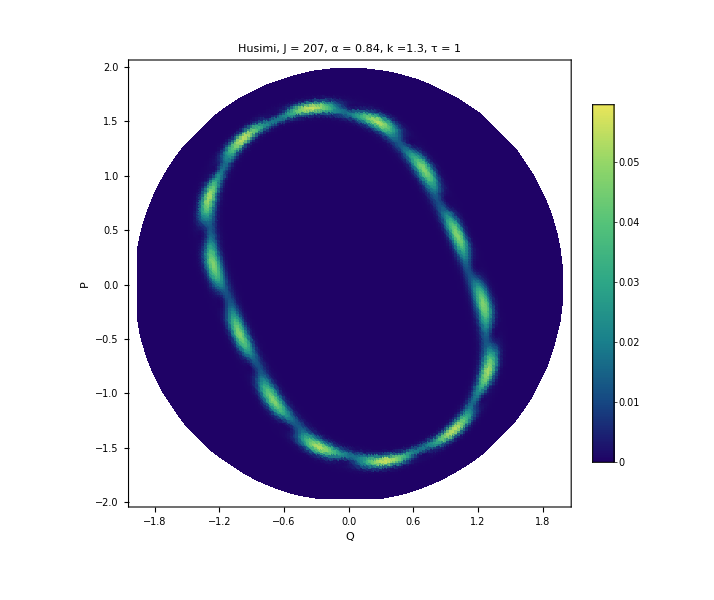

-Graphics-

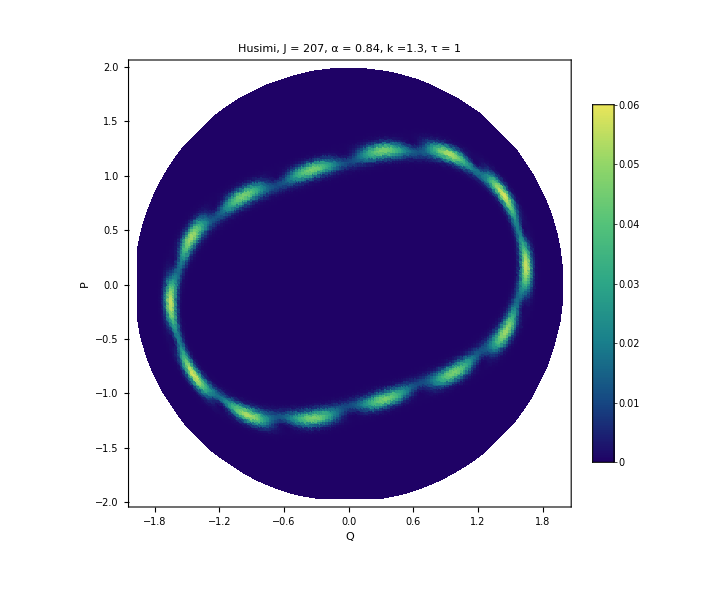

-Graphics-

```mathematica
ListDensityPlot[husistate1,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->1, PerformanceGoal->"Quality",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α2]]<>", k ="<>ToString[k2]<>", τ = "<>ToString[τ2],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
ListDensityPlot[husistate2,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->1, PerformanceGoal->"Quality",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α2]]<>", k ="<>ToString[k2]<>", τ = "<>ToString[τ2],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
ListDensityPlot[husistate3,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->1, PerformanceGoal->"Quality",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α2]]<>", k ="<>ToString[k2]<>", τ = "<>ToString[τ2],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
ListDensityPlot[husistate4,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->1, PerformanceGoal->"Quality",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α2]]<>", k ="<>ToString[k2]<>", τ = "<>ToString[τ2],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
```

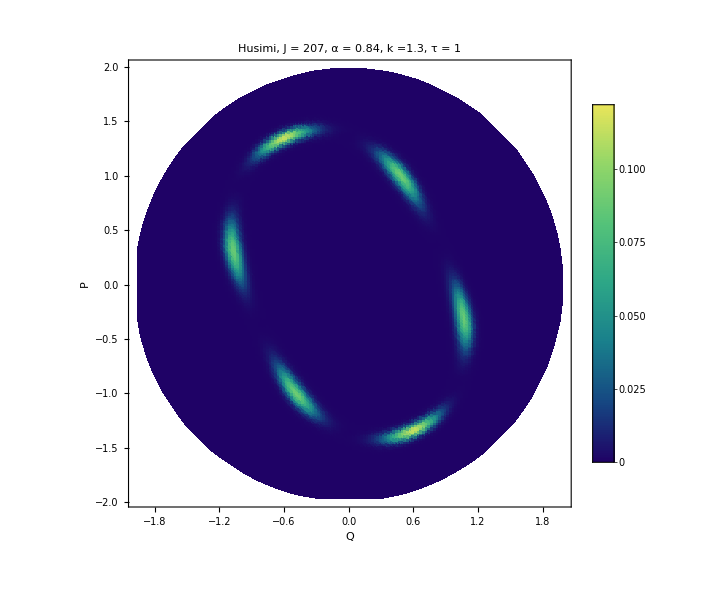

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListDensityPlot[husistate1,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->1, PerformanceGoal->"Quality",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α2]]<>", k ="<>ToString[k2]<>", τ = "<>ToString[τ2],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
ListDensityPlot[husistate2,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->1, PerformanceGoal->"Quality",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α2]]<>", k ="<>ToString[k2]<>", τ = "<>ToString[τ2],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
ListDensityPlot[husistate3,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->1, PerformanceGoal->"Quality",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α2]]<>", k ="<>ToString[k2]<>", τ = "<>ToString[τ2],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
ListDensityPlot[husistate4,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->1, PerformanceGoal->"Quality",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α2]]<>", k ="<>ToString[k2]<>", τ = "<>ToString[τ2],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
```

## D2 Statistics

```mathematica
newd2M=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2M]/Log[J+1]}];
```

```mathematica
ListPlot[Sort[newd2M[[All,3]]],PlotRange->All]
```

-Graphics-

```mathematica
Min[Sort[newd2M[[All,3]]]]
Max[Sort[newd2M[[All,3]]]]
```

0.736541

0.910626

```mathematica
bins=Range[0.72,0.95,0.02]
```

{0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94}

```mathematica
(*Classify data into bins*)
classifiedData=Table[Select[newd2M,bins[[i]]<=#[[3]]<bins[[i+1]]&],{i,Length[bins]-1}];
```

```mathematica
colors=ColorData["Rainbow"]/@Rescale[Most[bins]]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.2748607999999999, 0.1822636000000002, 0.7272788000000001],RGBColor[0.24848840000000008, 0.38632640000000046, 0.813373],RGBColor[0.2979596000000002, 0.5657928000000004, 0.7522385999999998],RGBColor[0.3882247999999999, 0.6741949999999999, 0.6035436000000002],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.6660832000000002, 0.7430418, 0.32293539999999993],RGBColor[0.8083416000000001, 0.7110805999999998, 0.2559759999999999],RGBColor[0.8935136000000002, 0.6004149999999995, 0.2205463999999999],RGBColor[0.8929546, 0.3896616000000002, 0.17940080000000005],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
(*Create a density plot for each category*)
Graphics[{Table[{colors[[i]],Point[classifiedData[[i,All,1;;2]]]},(*x,y coordinates*){i,Length[classifiedData]}]},PlotRange->All,PlotLabel->Style["J = "<>ToString[J],25,Black]]
```

-Graphics-

```mathematica
Graphics[{Table[{colors[[i]],Point[classifiedData[[i,All,1;;2]]]},(*x,y coordinates*){i,3}]},PlotRange->All,PlotLabel->Style["J = "<>ToString[J],25,Black]]
```

-Graphics-

```mathematica
filteredinitial=Transpose[{Flatten[classifiedData[[1;;3]],1][[All,1]],Flatten[classifiedData[[1;;3]],1][[All,2]]}];
ListPlot[filteredinitial,AspectRatio->1]
```

-Graphics-